# Calculation for Paper : "Enhancing silicon solar cells with singlet fission:the case for Förster resonant energy transfer using a quantum dot intermediate”

published in J.of Photonics for Energy, 8 (2), 022008 (2018) 
https : // doi.org/10.1117/1. JPE .8 .022008
Authors: Stefan Wil Tabernig; Benjamin Daiber; Tianyi Wang; Bruno Ehrler
		AMOLF
		Science Park 104
		1098XG
		Amsterdam
		The Netherlands
		
Corresponding Author: b.ehrler@amolf.nl

Published under GNU General Public License v3.0

## Load Directory

```mathematica
SetDirectory[NotebookDirectory[]]
Off[General::stop,NIntegrate::inumr,NIntegrate::nlim,NIntegrate::slwcon,NIntegrate::ncvb]
```

Y:\FRET Erratum\github

```mathematica
(*used files:
"OpticalPropertiesOfSilicon.xlsx"
"n_250-1450nm.txt"
"k_250-1450nm.txt"
".\\drawingintegration.png"
".\\Tc_PbS_cSi_geometry_no12.png"
".\\Jablonskidiagram.png"
*)
```

```mathematica
Get["CustomTicks`"]
```

## load constants

```mathematica
NAvogrado=6.022140857*10^23   (*mol^-1*);
c=299792458; (*m/s*)
epsilonOA=2.5 (*dielectric constant of oleic acid @ 20 deg; from http://www.clippercontrols.com/pages/Dielectric-Constant-Values.html*);
densitySi=2328 (*kg/m3 or g/l*);
molarmassSi=28.0855 (*g/mol*);
hbar=1.0545718*10^-34 (*Js*);
qelectron=1.602176628*10^-19(*c*);
eps0=8.854187817*10^-12(*F/m*);
(*FWHM = σ * 2.355*)
```

## Calculation of FRET efficiencies

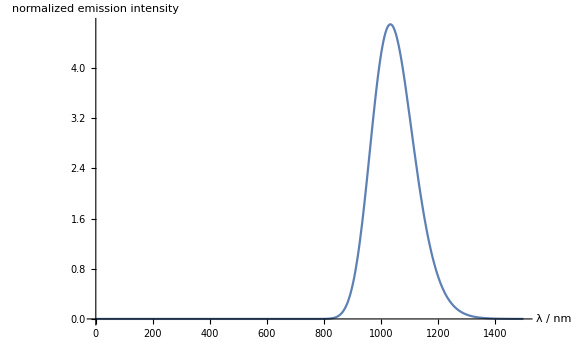

```mathematica
kappa2QD=2/3; (*... κ^2 for QDs. Comes from the assumption the the dipoles are randomly ordered.*) 
Etolam[En_]=1240/En;(*conversion formula from energy in eV to wavelength in nm. Works the other way around as well*)
dEtolam[En_,dEn_]=1240*dEn/En^2;  (*Δλ for converting Energies with associated errors to wavelengths, or the other way around*)

(*The following relations between QD size and Bandgap are taken from : Synthesis and characterization of quantum dots: A case study using PbS; DOI:10.1021*)

Ebg[d_]=0.41+1/(0.0252 d^2 + 0.283 d) (*Ebg... Bandgap in eV, d... QD diameter in nm*);
deltaEbg[d_]=(0.0252 d^2 + 0.283 d)^-2*(0.0504 d+0.283)*sigmad[d] (*calculation of the sigmaE from sigmad and d*);
dfunc1[En_]=-0.283/(0.0252*2)+Sqrt[(0.283/0.0252)^2+4/0.0252 1/(En-0.41)]/2;(*dfunc1 is a function that back converts the Bandgap to QD size. Needed because a lot of functions I made require the QD size instead of the bandgap*)
sigmadpc=0.07  (*relative deviation of the diameter d in % (actually between 6.8 and 8.6 depending on size)*);
sigmad[d_]=sigmadpc*d (*absolute value of the diameter deviation in nm *);
engausssss[En_,d_]=PDF[NormalDistribution[Ebg[d],deltaEbg[d]],En];(*Gaussian distribution of the bandgap as function of Energy and QD size (d..diameter)*)

(*in the following calculations, we won't use the quantum dot size or the first exciton peak energy but the emission energy*)
IDPbS[Envar_,ebgvar_]=PDF[NormalDistribution[ebgvar,0.2/2.355],Envar];(*Gaussian distribution of the emission energy with a FWHM of 0.2 eV and a σ of 0.2/2.355 eV*)
Plot[IDPbS[Etolam[x],1.2],{x,0,1500},PlotRange->All,AxesLabel->{"λ / nm","normalized emission intensity"}]
```

### molar absorption (/extinction / attenuation) coefficient α_(molar,Si)

#### The literature is not consistent at all when it comes to this quantity. Still, after comparison with other calculations it becomes obvious that one can get to this quantity by dividing the absorption coefficient of Si by its molar concentration.

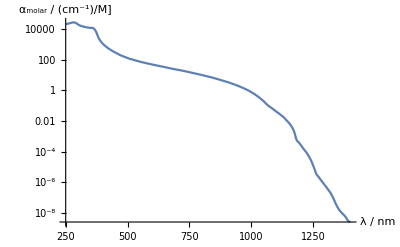

```mathematica
molarConcentration[density_,molarmass_]=density/molarmass(*mol per volume; density in grams per Volume; molarmass in grams per mol; final units in M (Molar=mol/litre)*);
rawdataSi=Import["OpticalPropertiesOfSilicon.xlsx"](*getting data for Si*);
rawdataSin=Import[".\\n_250-1450nm.txt","Table"](*getting data for Si*);
rawdataSik=Import[".\\k_250-1450nm.txt","Table"](*getting data for Si*);
rawdataSi[[1]][[All,4]]=rawdataSin[[All,2]];
rawdataSi[[1]][[All,5]]=rawdataSik[[All,2]];
(*above, k and n were taken from a different source as the initial source does not cover enough digits for k, which means that it is zero across a wide range although it should still have a specific value not equal to 0.*)

abscoefficientSi=Table[{rawdataSi[[1]][[i]][[1]],rawdataSi[[1]][[i]][[2]]},{i,2,Length[rawdataSi[[1]]]-1}](*reducing data to a wavelength and an absorption coefficient column α(λ) (units of cm-1(nm)). (from 250 nm to 1400 nm)*);
absCoeffSi=Interpolation[abscoefficientSi](*making a function out of it; *);
molarAbsCoeffSi[lam_]=absCoeffSi[lam]/molarConcentration[densitySi,molarmassSi] (*getting the molarabsorption coefficient by division with the molar concentration of crystalline Si*);
LogPlot[molarAbsCoeffSi[x],{x,250,1400},PlotRange->All,AxesLabel->{"λ / nm","α_molar / cm^-1/M]"}](*figure to the formula above*)
```

### Overlap integral J_overlap: J_overlap=∫ϕ_D(λ)*α_(molar,Si)(λ)*λ^4 dλ

#### The formula above does not include the refractive index n for the spacer material yet, because it was initially assumed to be constant across the investigated spectrum.

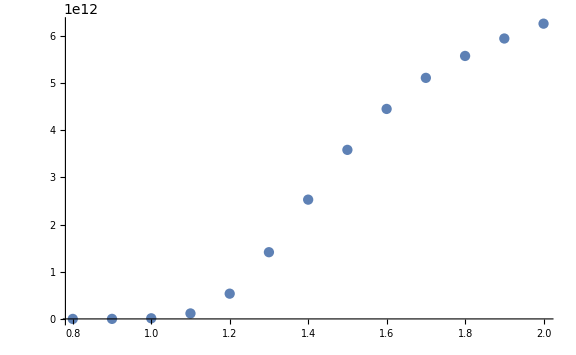

```mathematica
Joverlap[En_]=NIntegrate[IDPbS[Etolam[lam],En]*molarAbsCoeffSi[lam]*lam^4,{lam,250,1450}]/NIntegrate[IDPbS[Etolam[x],En],{x,0,1600}];
ListPlot[Table[{i,Joverlap[i]},{i,0.8,2,0.1}]](*overlap integral of donor emission, molar acceptor absorption coefficient and lambda^4 in units of nm^4/(cm M)*) 

(*the following plot is a plot for J as function of the bandgap. Takes a while to evaluate, thus taken out.

ListLogPlot[Table[{Ebg[i],Joverlap[i]},{i,0.5,6,0.05}]]

*)
```

### R_0-Foerster distance

```mathematica
R0[quantumyielddonor_,En_]=0.0211*(kappa2QD*quantumyielddonor/1.45^4 Joverlap[En])^(1/6);(*This is the formula for the foerster distance given in countless books and papers. In some cases the pre factors differ depending on the choice of units though. Kappa2QD is the square of the orientation factor, the quantumyield is a variable and the 1.45 stands for the refractive index of SiO2. *)
```

```mathematica
R0test1=Table[{i,R0[1,i]},{i,0.8,2,0.05}];
R0test0p55=Table[{i,R0[0.55,i]},{i,0.8,2,0.05}];
R0test0p2=Table[{i,R0[0.2,i]},{i,0.8,2,0.05}];(*That is a produced list with foerster distance depending on the bandgap. The running variable is the emission energy.*)
```

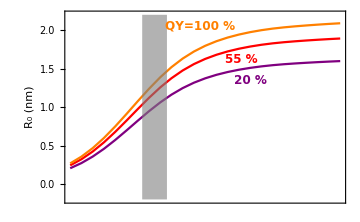

foersterdistanceshaded.png

```mathematica
foersterdistanceplot=ListPlot[{R0test0p2,R0test0p55,R0test1},PlotRange->{{0.8,2},{-0.2,2.2}},Frame->True,FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{StripTickLabels[LinTicks],LinTicks}},FrameTicksStyle->{{Black,Black},{Directive[FontOpacity->0,FontSize->0,Black],Black}},FrameLabel->{{"R_0 (nm)",},{ ,}},LabelStyle->{Bold,Larger,Black},ImageSize->Medium,Joined->True,GridLinesStyle->Directive[DotDashed,Black,Thickness[0.005]],PlotStyle->{Purple,Red,Orange},ImagePadding->{{50,50},{0,50}},Epilog->{Text[Style["QY=100 %",12,Orange,Bold],Scaled[{0.48,0.92}]],Text[Style["55 %",12,Red,Bold],Scaled[{0.63,0.75}]],Text[Style["20 %",12,Purple,Bold],Scaled[{0.66,0.64}]]}];
shadedarea=Graphics[{Opacity[0.6],Gray,Rectangle[{1.12,-0.2},{1.23,2.2}]}];
foersterdistanceplotshaded=Show[foersterdistanceplot,shadedarea]
Export["foersterdistanceshaded.png",foersterdistanceplotshaded](*plot shows the change of Subscript[R, 0] as function of emission energy*)
```

### η_FRET... Foerster transfer efficiency

```mathematica
Efret[rfoerster_,rdonoracceptor_]=rfoerster^6/(rfoerster^6+rdonoracceptor^6);(*Foerster transfer efficiency for the point dipole - point dipole case*)
EtaFRET[kFRETvar_]=kFRETvar/(1+kFRETvar);(*general formula for the FRET efficiency*)
```

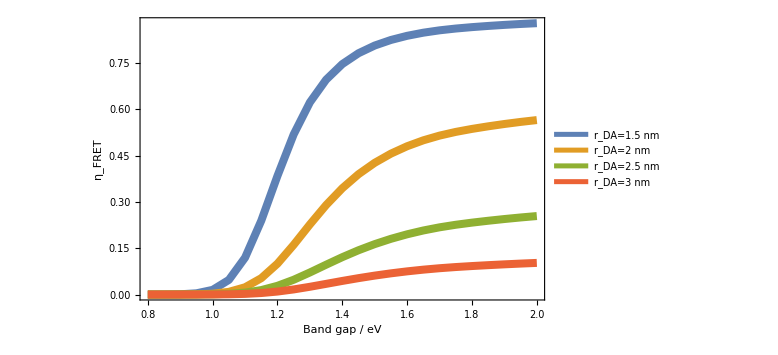

..\presentations\foersterefficiency.png

```mathematica
foersterefficiencyplot=ListPlot[{Table[{i,Efret[R0test1[[Round[-15+20*i]]][[2]],1.5]},{i,0.8,2,0.05}],Table[{i,Efret[R0test1[[Round[-15+20*i]]][[2]],2]},{i,0.8,2,0.05}],Table[{i,Efret[R0test1[[Round[-15+20*i]]][[2]],2.5]},{i,0.8,2,0.05}],Table[{i,Efret[R0test1[[Round[-15+20*i]]][[2]],3]},{i,0.8,2,0.05}]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Table[{i,N[Round[dfunc1[i],10^-1]]},{i,1,R0test1[[-1]][[1]]}]}},PlotLegends->Placed[{"r_DA=1.5 nm","r_DA=2 nm","r_DA=2.5 nm","r_DA=3 nm"},{0.15,0.7}],FrameLabel->{{"η_FRET","η_FRET"},{"Band gap / eV","QD size / nm"}},LabelStyle->{Bold,Larger},PlotStyle->Thickness[0.01],ImageSize->Large,Joined->True]
Export["..\\presentations\\foersterefficiency.png",foersterefficiencyplot]
```

```mathematica
(*the plot above shows the FRET efficiencies for different DA spacings as a function of QD emission*)
```

### Foerster Transfer rate k_FRET

```mathematica
atomicDensity3DSi=50 (*atoms * nm^-3*); 
atomicDensity2DSi=7.8 (*atoms * nm^-2, 111 crystal orientation*);
```

```mathematica
k6FRETnorm[rDA_,R0var_]:=(R0var/rDA)^6;(*FRET rate for the point dipole - point dipole model*)
k4Fretn[rDAvar_,R0var_]:=atomicDensity2DSi π/2 R0var^6/rDAvar^4;(*FRET rate for the point dipole - infinite plane model*)
k3Fretn[rDAvar_,R0var_]:=atomicDensity3DSi π/6 1.45/3.55 R0var^6/rDAvar^3;(*1.45/3.55 ... Subscript[n, SP]/Subscript[n, Si]; FRET rate for the point dipole - bulk over half space model including a correction for the refractive index of the separating medium*)

(*the formulas above are "normalized", which in this case does not mean that their integral equals 1 but that the scaling prefactor 1/Subscript[τ, 0] is missing.*)
```

## QD absorption, PL, Si absorption coeff (molar) +Inset time resolved PL QD

{1.2eV1mgpml100pc5min.dat,1.5eV1mgpml100pc5min.dat}

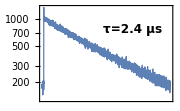

QDlifetimesinOctane.png

```mathematica
filenamesPCmeasurement041017=FileNames["*100pc5min.dat"](*loading a list with the lifetime filenames *)
PCmeasurement041017list=
Table[{FileBaseName[filenamesPCmeasurement041017[[i]]],Import[FileNameJoin[{".",filenamesPCmeasurement041017[[i]]}],"Table","NumberPoint"->","]},{i,1,Length[filenamesPCmeasurement041017]}];(*loading the content of the files and plugging them together with the filenames, so that they are "labelled" within the list*)
PCmeasurement041017figure=ListLogPlot[{PCmeasurement041017list[[1]][[2]][[3;;Length[PCmeasurement041017list[[1]][[2]]]-1]][[All,{1,2}]]},PlotRange->All,Frame->True,Joined->True,FrameLabel->{{"PL-Counts",None},{None,"t (μs)"}},FrameTicks->{{All,None},{None,All}},LabelStyle->{Black,Bold,10},PlotStyle->Thickness[0.005],ImageSize->180,Epilog->{Text[Style["τ=2.4 μs",12,Bold],Scaled[{0.7,0.75}]]}](*creating the figure*)
Export["QDlifetimesinOctane.png",PCmeasurement041017figure](*saving it as a .png file (png is recommended for use in LaTeX files*)
```

```mathematica
(*figure shows the PL decay of 1.2 eV PbS QDs in octane solution. resized to fit as an inset*)
```

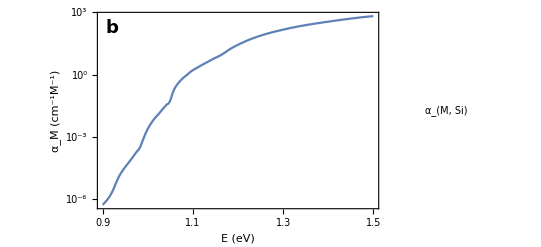

spectrainsetplot.png

```mathematica
SetOptions[LogTicks,LogPlot->False];
spectrainsetplot=Plot[{Log10[absCoeffSi[Etolam[x]]]},{x,0.9,1.5},Frame->True,FrameTicks->{{LogTicks[10,-6,3,TickLabelStep->3,ShowMinorTicks->False],StripTickLabels[LinTicks]},{LinTicks,StripTickLabels[LinTicks]}},FrameTicksStyle->Black,PlotLegends->Placed[LineLegend[{White},{"α_(M, Si)"},LegendLayout->{"Column",1}],{0.25,0.76}],Axes->False,FrameLabel->{{"α_M (cm^-1M^-1)",},{"E (eV)",}},LabelStyle->{Bold,Larger,Black},PlotStyle->{{},{ColorData[97,"ColorList"][[3]],Dashed}},ImageSize->400,Epilog->{Inset[PCmeasurement041017figure,Scaled[{0.67,0.35}]],Text[Style["b",18,Bold],Scaled[{0.05,0.92}]]}]
Export["spectrainsetplot.png",spectrainsetplot]
```

```mathematica
(*figure shows Si absorption coefficient on a log scale with the PL decay of the PbS QDs as an inset*)
```

### extra figure

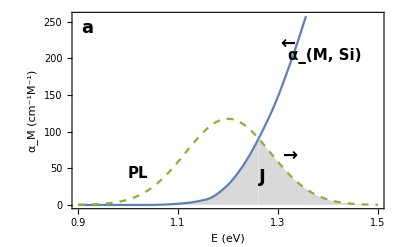

./abscoeffSimolarLINEAR.png

```mathematica
absCoeffSilinplot=Plot[{absCoeffSi[Etolam[x]],25 IDPbS[x,1.2],ConditionalExpression[#,#≥0]&[Min[absCoeffSi[Etolam[x]],25IDPbS[x,1.2]]]},{x,0.9,1.5},Frame->True,FrameTicksStyle->Black,PlotLegends->None,FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks,StripTickLabels[LinTicks]}},FrameLabel->{{"α_M (cm^-1M^-1)","PL"},{"E (eV)",}},LabelStyle->{Bold,Larger,Black},PlotStyle->{{},{ColorData[97,"ColorList"][[3]],Dashed},None},ImageSize->400,Filling-> {3->{Axis,LightGray}},Epilog->{Text[Style["←",18,Bold],Scaled[{0.69,0.84}]],Text[Style["→",18,Bold],Scaled[{0.7,0.27}]],Text[Style["J",18,Bold],Scaled[{0.61,0.16}]],Text[Style["α_(M, Si)",15,Bold],Scaled[{0.81,0.78}]],Text[Style["PL",15,Bold],Scaled[{0.21,0.18}]],Text[Style["a",18,Bold],Scaled[{0.05,0.92}]]}];
absCoeffSilinplotpluscirc=Show[absCoeffSilinplot]
Export["./abscoeffSimolarLINEAR.png",absCoeffSilinplotpluscirc]
```

```mathematica
(*figure shows the QD PL (a.u.) and the absorption coefficient of Si in order to indicate the overlap, which is hinted at with the "J"*)
```

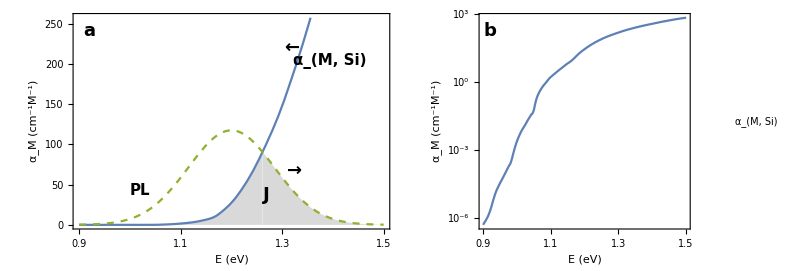

FRETfig2.png

```mathematica
absCoeffLinplusLog=GraphicsRow[{absCoeffSilinplotpluscirc,spectrainsetplot},Spacings->0]
Export["FRETfig2.png",absCoeffLinplusLog,ImageResolution->300]
```

## paper: η_FRET for different distance dependencies + PL lifetime inset

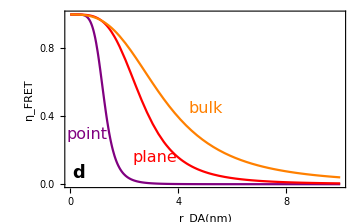

```mathematica
R0q0p2bg1p2=R0[0.2,1.2];
R0q0p55bg1p2=R0[0.55,1.2];
R0q1bg1p2=R0[1,1.2];
etafretR0anddistancedep=Plot[{EtaFRET[k6FRETnorm[x,R0q0p55bg1p2]],EtaFRET[k4Fretn[x,R0q0p55bg1p2]],EtaFRET[k3Fretn[x,R0q0p55bg1p2]]},{x,0,10},PlotRange->All,Frame->True,FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks,StripTickLabels[LinTicks]}},PlotLegends->Placed[LineLegend[{"r_DA^-6","r_DA^-4","r_DA^-3"},LegendLayout->{"Column",1}],{0.13,0.2}],FrameLabel->{{"η_FRET"},{"r_DA/ nm"}},LabelStyle->{Bold,Larger,Black},PlotStyle->{Purple,Blue,ColorData[97,"ColorList"][[1]]},ImageSize->Large];
etafretR0anddistancedepinset=Plot[{EtaFRET[k6FRETnorm[x,R0q0p55bg1p2]],EtaFRET[k4Fretn[x,R0q0p55bg1p2]],EtaFRET[k3Fretn[x,R0q0p55bg1p2]]},{x,0,10},PlotRange->All,Frame->True,FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks,StripTickLabels[LinTicks]}},FrameTicksStyle->Black,FrameLabel->{{"η_FRET",},{"r_DA(nm)",}},LabelStyle->{Bold,Larger,Black},PlotStyle->{Purple,Red,Orange},ImageSize->Medium,Epilog->{Text[Style["point",16,Purple],Scaled[{0.08,0.3}]],Text[Style["plane",16,Red],Scaled[{0.32,0.17}]],Text[Style["bulk",16,Orange],Scaled[{0.5,0.45}]],Text[Style["d",18,Bold],Scaled[{0.05,0.08}]]}]
Export["paper_FRETefficiencyR0,RDAinset.png",etafretR0anddistancedepinset,ImageResolution->300];
```

```mathematica
(*figure shows distance dependence of the different FRET models *)
```

```mathematica
drawint=Import[".\\drawingintegration.png"];
fig5=GraphicsRow[{drawint,etafretR0anddistancedepinset},Spacings->-30]
Export["FRETfig5.png",fig5,ImageResolution->300]
```

-Graphics-

FRETfig5.png

## Fig.1

```mathematica
geometryfig=Import[".\\Tc_PbS_cSi_geometry_no12.png"];
jablonskifig=Import[".\\Jablonskidiagram.png"];
fig1=GraphicsRow[{geometryfig,jablonskifig}]
Export["FRETfig1.png",fig1,ImageResolution->300]
```

-Graphics-

FRETfig1.png

```mathematica
(*Figures illustrate the geometry and the corresponding jablonski diagram*)
```

## paper: η_FRET bandgap (size dependance) at different distances

```mathematica
R0list0p2=Table[{i,R0[0.2,i]},{i,0.1,2.5,0.05}];
R0list0p55=Table[{i,R0[0.55,i]},{i,0.1,2.5,0.05}];
R0list1p0=Table[{i,R0[1,i]},{i,0.1,2.5,0.05}];
(*lists for varying PLQYs*)
```

```mathematica
foersterefficiency6BGlist={Table[{i,k6FRETnorm[2,R0list0p2[[Round[-1+20*i]]][[2]]]/(1+k6FRETnorm[2,R0list0p2[[Round[-1+20*i]]][[2]]])},{i,0.1,2.5,0.05}],Table[{i,k6FRETnorm[1,R0list0p2[[Round[-1+20*i]]][[2]]]/(1+k6FRETnorm[1,R0list0p2[[Round[-1+20*i]]][[2]]])},{i,0.1,2.5,0.05}],Table[{i,k6FRETnorm[2,R0list0p55[[Round[-1+20*i]]][[2]]]/(1+k6FRETnorm[2,R0list0p55[[Round[-1+20*i]]][[2]]])},{i,0.1,2.5,0.05}],Table[{i,k6FRETnorm[1,R0list0p55[[Round[-1+20*i]]][[2]]]/(1+k6FRETnorm[1,R0list0p55[[Round[-1+20*i]]][[2]]])},{i,0.1,2.5,0.05}],Table[{i,k6FRETnorm[2,R0list1p0[[Round[-1+20*i]]][[2]]]/(1+k6FRETnorm[2,R0list1p0[[Round[-1+20*i]]][[2]]])},{i,0.1,2.5,0.05}],Table[{i,k6FRETnorm[1,R0list1p0[[Round[-1+20*i]]][[2]]]/(1+k6FRETnorm[1,R0list1p0[[Round[-1+20*i]]][[2]]])},{i,0.1,2.5,0.05}]};
foersterefficiency4BGlist={Table[{i,k4Fretn[2,R0list0p2[[Round[-1+20*i]]][[2]]]/(1+k4Fretn[2,R0list0p2[[Round[-1+20*i]]][[2]]])},{i,0.1,2.5,0.05}],Table[{i,k4Fretn[1,R0list0p2[[Round[-1+20*i]]][[2]]]/(1+k4Fretn[1,R0list0p2[[Round[-1+20*i]]][[2]]])},{i,0.1,2.5,0.05}],Table[{i,k4Fretn[2,R0list0p55[[Round[-1+20*i]]][[2]]]/(1+k4Fretn[2,R0list0p55[[Round[-1+20*i]]][[2]]])},{i,0.1,2.5,0.05}],Table[{i,k4Fretn[1,R0list0p55[[Round[-1+20*i]]][[2]]]/(1+k4Fretn[1,R0list0p55[[Round[-1+20*i]]][[2]]])},{i,0.1,2.5,0.05}],Table[{i,k4Fretn[2,R0list1p0[[Round[-1+20*i]]][[2]]]/(1+k4Fretn[2,R0list1p0[[Round[-1+20*i]]][[2]]])},{i,0.1,2.5,0.05}],Table[{i,k4Fretn[1,R0list1p0[[Round[-1+20*i]]][[2]]]/(1+k4Fretn[1,R0list1p0[[Round[-1+20*i]]][[2]]])},{i,0.1,2.5,0.05}]};
foersterefficiency3BGlist={Table[{i,k3Fretn[2,R0list0p2[[Round[-1+20*i]]][[2]]]/(1+k3Fretn[2,R0list0p2[[Round[-1+20*i]]][[2]]])},{i,0.1,2.5,0.05}],Table[{i,k3Fretn[1,R0list0p2[[Round[-1+20*i]]][[2]]]/(1+k3Fretn[1,R0list0p2[[Round[-1+20*i]]][[2]]])},{i,0.1,2.5,0.05}],Table[{i,k3Fretn[2,R0list0p55[[Round[-1+20*i]]][[2]]]/(1+k3Fretn[2,R0list0p55[[Round[-1+20*i]]][[2]]])},{i,0.1,2.5,0.05}],Table[{i,k3Fretn[1,R0list0p55[[Round[-1+20*i]]][[2]]]/(1+k3Fretn[1,R0list0p55[[Round[-1+20*i]]][[2]]])},{i,0.1,2.5,0.05}],Table[{i,k3Fretn[2,R0list1p0[[Round[-1+20*i]]][[2]]]/(1+k3Fretn[2,R0list1p0[[Round[-1+20*i]]][[2]]])},{i,0.1,2.5,0.05}],Table[{i,k3Fretn[1,R0list1p0[[Round[-1+20*i]]][[2]]]/(1+k3Fretn[1,R0list1p0[[Round[-1+20*i]]][[2]]])},{i,0.1,2.5,0.05}]};
```

```mathematica
paperfoersterefficiencyplot6=ListPlot[foersterefficiency6BGlist,Frame->True,Frame->True,FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks,StripTickLabels[LinTicks]}},FrameTicksStyle->{{Black,Black},{Black,Directive[Black,FontOpacity->0,FontSize->0]}},FrameLabel->{{"η_FRET",},{"QD Bandgap (eV)", }},LabelStyle->{Bold,Larger,Black},PlotStyle->{Purple,{Purple,Dashed},Red,{Red,Dashed},Orange,{Orange,Dashed}},ImageSize->Medium,Joined->True,PlotRange->{{0.8,2},{0,1.10}},ImagePadding->{{50,50},{50,0}},Epilog->{Text[Style["r_DA= 1 nm",10,Bold],Scaled[{0.67,0.72}]],Text[Style["r_DA= 2 nm",10,Bold],Scaled[{0.49,0.45}]]}];
shadedarea=Graphics[{Opacity[0.6],Gray,Rectangle[{1.12,-2},{1.23,7}]}];
ellipse1nm=Graphics[{Opacity[0],EdgeForm[Directive[Thickness[0.002]]],Rotate[Disk[{1.6,0.95},{0.07,0.09}],50 Degree]}];
ellipse2nm=Graphics[{Opacity[0],EdgeForm[Directive[Thickness[0.002]
]],Rotate[Disk[{1.4,0.23},{0.08,0.2}],15  Degree]}];
paperfoersterefficiencyplotshaded6=Show[paperfoersterefficiencyplot6,shadedarea,ellipse1nm,ellipse2nm]
Export["paper_foersterefficiencyBGdepshaded6.png",paperfoersterefficiencyplotshaded6]
```

-Graphics-

paper_foersterefficiencyBGdepshaded6.png

```mathematica
(*plot for 6th power depenence*)
```

```mathematica
r0plusfretplotsshaded=Column[{foersterdistanceplotshaded,paperfoersterefficiencyplotshaded6},Spacings->0]
Export["./FRETfig3.png",r0plusfretplotsshaded,ImageResolution->300]
```

-Graphics-

./FRETfig3.png

```mathematica
paperfoersterefficiencyplot4=ListPlot[foersterefficiency4BGlist,Frame->True,FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{StripTickLabels[LinTicks],LinTicks}},FrameTicksStyle->{{Black,Black},{Directive[Black,FontOpacity->0,FontSize->0],Black}},FrameLabel->{{"η_FRET",},{, }},LabelStyle->{Bold,Larger,Black},PlotStyle->{Purple,{Purple,Dashed},Red,{Red,Dashed},Orange,{Orange,Dashed}},ImageSize->Medium,Joined->True,PlotRange->{{0.8,2},{-0.05,1.10}},ImagePadding->{{50,50},{0,50}},Epilog->{Text[Style["r_DA= 1 nm",10,Bold],Scaled[{0.45,0.95}]],Text[Style["r_DA= 2 nm",10,Bold],Scaled[{0.45,0.45}]],Text[Style["plane",18,Bold],Scaled[{0.12,0.9}]]}];
shadedarea4=Graphics[{Opacity[0.6],Gray,Rectangle[{1.12,-2},{1.23,1.1}]}];
ellipse1nm4=Graphics[{Opacity[0],EdgeForm[Directive[Thickness[0.002]]],Rotate[Disk[{1.15,0.96},{0.05,0.07}],50 Degree]}];
ellipse2nm4=Graphics[{Opacity[0],EdgeForm[Directive[Thickness[0.002]
]],Rotate[Disk[{1.22,0.73},{0.06,0.15}],15  Degree]}];
paperfoersterefficiencyplotshaded4=Show[paperfoersterefficiencyplot4,shadedarea4,ellipse1nm4,ellipse2nm4]
Export["paper_foersterefficiencyBGdepshaded4.png",paperfoersterefficiencyplotshaded4];


paperfoersterefficiencyplot3=ListPlot[foersterefficiency3BGlist,Frame->True,Frame->True,FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks,StripTickLabels[LinTicks]}},FrameTicksStyle->{{Black,Black},{Black,Directive[FontOpacity->0,FontSize->0]}},FrameLabel->{{"η_FRET",},{"QD Bandgap (eV)", }},LabelStyle->{Bold,Larger,Black},PlotStyle->{Purple,{Purple,Dashed},Red,{Red,Dashed},Orange,{Orange,Dashed}},ImageSize->Medium,Joined->True,PlotRange->{{0.8,2},{-0.05,1.10}},ImagePadding->{{50,50},{50,0}},Epilog->{Text[Style["r_DA= 1 nm",10,Bold],Scaled[{0.32,0.95}]],Text[Style["r_DA= 2 nm",10,Bold],Scaled[{0.47,0.65}]],Text[Style["bulk",18,Bold],Scaled[{0.12,0.9}]]}];
shadedarea3=Graphics[{Opacity[0.6],Gray,Rectangle[{1.12,-2},{1.23,7}]}];
ellipse1nm3=Graphics[{Opacity[0],EdgeForm[Directive[Thickness[0.002]]],Rotate[Disk[{1.11,0.9},{0.05,0.08}],15 Degree]}];
ellipse2nm3=Graphics[{Opacity[0],EdgeForm[Directive[Thickness[0.002]
]],Rotate[Disk[{1.25,0.85},{0.06,0.10}],15  Degree]}];
paperfoersterefficiencyplotshaded3=Show[paperfoersterefficiencyplot3,shadedarea3,ellipse1nm3,ellipse2nm3]
Export["paper_foersterefficiencyBGdepshaded3.png",paperfoersterefficiencyplotshaded3];

columnplot3and4=Column[{paperfoersterefficiencyplotshaded4,paperfoersterefficiencyplotshaded3},Spacings->0]
Export["FRETfig4.png",columnplot3and4,ImageResolution->300]
```

-Graphics-

-Graphics-

-Graphics-

FRETfig4.png

```mathematica
(*plots for 4th and 3rd power dependence*)
```